```mathematica
Plot3D[x^2 + y^2, {x, -1.2, 1.2}, {y, -1.2, 1.2}]
```

-Graphics3D-

```mathematica
Show[%1,AxesStyle->Gray]
```

-Graphics3D-

```mathematica
Show[%2,Background->None]
```

-Graphics3D-

```mathematica
Plot3D[x^2 + y^2, {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

```mathematica
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},Mesh->Automatic,MeshFunctions->Automatic,Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
Show[%6,ViewPoint->{0,-∞,0}]
```

-Graphics3D-

```mathematica
Show[%7,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[%8,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Show[%9,ViewPoint->Left]
```

-Graphics3D-

```mathematica
Show[%10,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[%11,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
f =Function[x,y, x*x + y * x]
```

Attributes::attnf: x x+y x is not a known attribute.

Function[x,y,x x+y x]

```mathematica
f[x,y]
```

Attributes::attnf: x x+y x is not a known attribute.

Function[x,y,x x+y x][x,y]

```mathematica
f
```

Function[x,y,x x+y x]

```mathematica
f = Function[x_, y_, x_^2 + y_^2]
```

Function::flpar: Parameter specification x_ in Function[x_,y_,x_^2+y_^2] should be a symbol or a list of symbols.

Function[x_,y_,x_^2+y_^2]

```mathematica
g[x_, y_] := x^2+y^2
```

```mathematica
g[0,1]
```

1

```mathematica
g[20,10]
```

500

```mathematica
FactorInteger[500]
```

{{2,2},{5,3}}

```mathematica
Plot3D[g[x, y], {x, -3, 3}, {y, -3, 3}, Filling->Axis]
```

-Graphics3D-

```mathematica
Integrate[g[x, y],{x,-2,2}, {y, -3, 3}]
```

104

```mathematica
Plot3D[g[x, y],{x,-3,3},{y,-3,3},RegionFunction->(-2<#1 <2 && -2 <#2<2 &),Filling->Bottom,FillingStyle->Opacity[0.7],Mesh-> None]
```

-Graphics3D-

```mathematica
Plot3D[g[x,y],{x,-3,3},{y,-3,3},Mesh->None,RegionFunction->(-2<#1<2&&-2<#2<2&),Filling->Bottom,FillingStyle->Opacity[0.7],Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[g[x,y],{x,-3,3},{y,-3,3},Mesh->Automatic,MeshFunctions->Automatic,Mesh->None,RegionFunction->(-2<#1<2&&-2<#2<2&),Filling->Bottom,FillingStyle->Opacity[0.7],Mesh->None]
```

-Graphics3D-

```mathematica
Show[%42,Axes->False]
```

-Graphics3D-

```mathematica
Show[%43,Axes->True,AxesStyle->Black]
```

-Graphics3D-

```mathematica
Rasterize[%44,"Image"]
```

-Graphics-

```mathematica
Rasterize[%44,"Image"]
```

```mathematica
Export["/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/x2+y2.png",%44,"PNG"]
```

```mathematica
"/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/x2+y2.png"
```

```mathematica
"/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/x2+y2.png"
```

/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/x2+y2.png

```mathematica
g[x_, y_] := y*e^-x
```

```mathematica
Plot3D[y*E^-x,{x,0,3},{y,0,3},Mesh->Automatic,MeshFunctions->Automatic,Mesh->None,RegionFunction->(#1<#2&),Filling->Bottom,FillingStyle->Opacity[0.7],Mesh->None]
```

```mathematica
-Graphics3D-
Export["/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/ye-x.png", -Graphics3D-, "PNG", ImageSize->200]
```

-Graphics3D-

/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/ye-x.png

```mathematica
Show[%25,ViewPoint->Left]
```

-Graphics3D-

```mathematica
Rasterize[%25,"Image"]
```

-Graphics-

```mathematica
Export["/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/ye-x.png",%25,"PNG"]
```

/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/ye-x.png

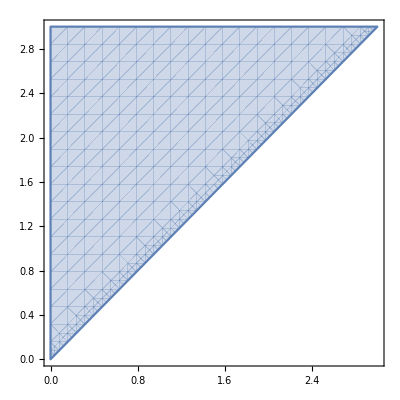

```mathematica
RegionPlot[y > x && x > 0 && y <  3,{x, 0, 3},{y,0, 3}]
```

```mathematica
Show[%28,Axes->True]
```

-Graphics-

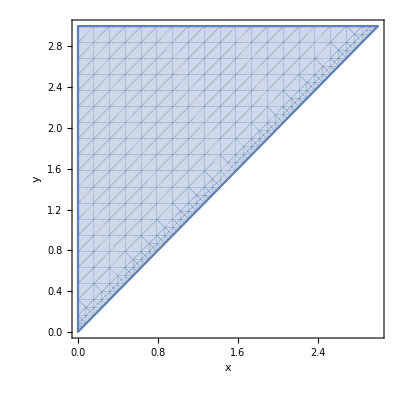

```mathematica
Show[%29,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->None,LabelStyle->{FontFamily->"Al Bayan",GrayLevel[0]}]
```

```mathematica
Export["/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/boundary.png",%30,"PNG"]
```

/Users/tylerzhu/Dropbox/Berkeley/CS 70/calc_review/boundary.png

```mathematica
Show[%30,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

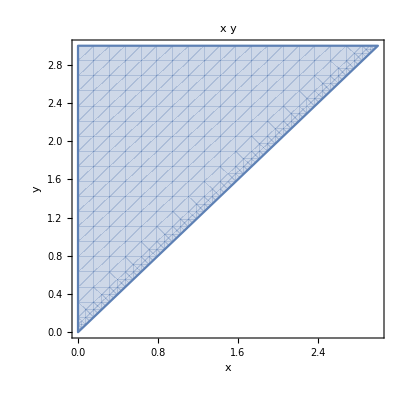

```mathematica
Show[%32,PlotLabel->HoldForm[x y]]
```

```mathematica
Show[%33,PlotLabel->None]
```

-Graphics-